```mathematica
FullSimplify[(u+d)/(1-u d)/.u->Sin[θ]/(γ(β+Cos[θ]))/.d->Sin[θ]/(γ(β-Cos[θ]))]
```

(2 β γ Sin[θ])/(γ^2 (β^2-Cos[θ]^2)-Sin[θ]^2)

```mathematica
TrigReduce[(2 β γ Sin[θ])/(γ^2 (β^2-Cos[θ]^2)-Sin[θ]^2)]
```

(4 β γ Sin[θ])/(-1-γ^2+2 β^2 γ^2+Cos[2 θ]-γ^2 Cos[2 θ])

```mathematica
Solve[Tan[θ]==(2x)/(x^2-1),x]
```

{{x→Cot[θ/2]},{x→-Tan[θ/2]}}

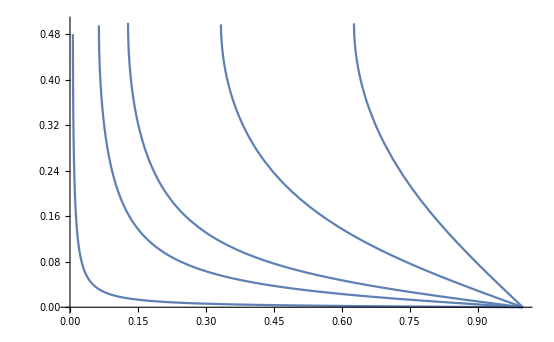

```mathematica
Plot[ArcSin[Cot[π θ/2]/(√(γ^2-1))/.γ->{1.2,2,5,10,100}]/π,{θ,0,1}]
```

```mathematica
D[ArcSin[Cot[θ/2]/(√(γ^2-1))],θ]
```

-Csc[θ/2]^2/(2 √(-1+γ^2) √(1-Cot[θ/2]^2/(-1+γ^2)))

```mathematica
Simplify[-Csc[θ/2]^2/(2 √(-1+γ^2) √(1-Cot[θ/2]^2/(-1+γ^2)))]
```

-Csc[θ/2]^2/(2 √(-1+γ^2) √(1-Cot[θ/2]^2/(-1+γ^2)))